ΜΣΜ 61  
2η Γραπτή Εργασία
Λυμπερίδης Σταύρος   Α.Μ.: 91076

Ασκηση 1

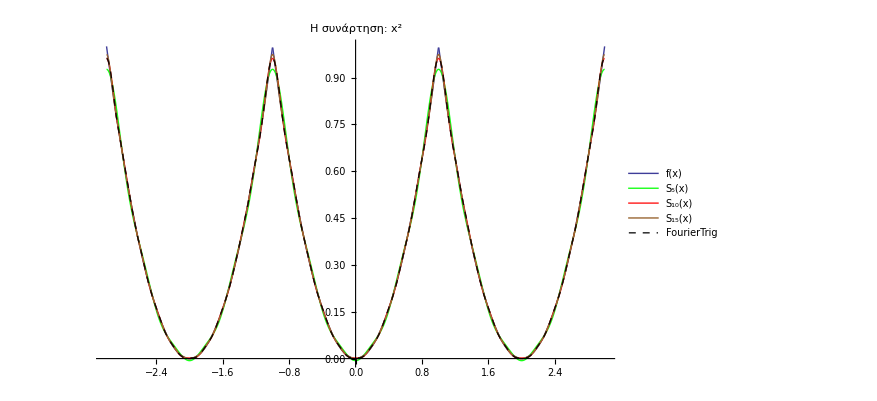

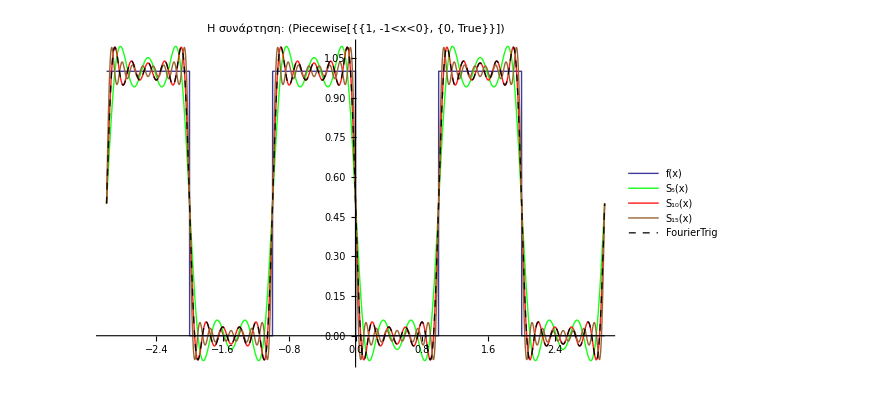

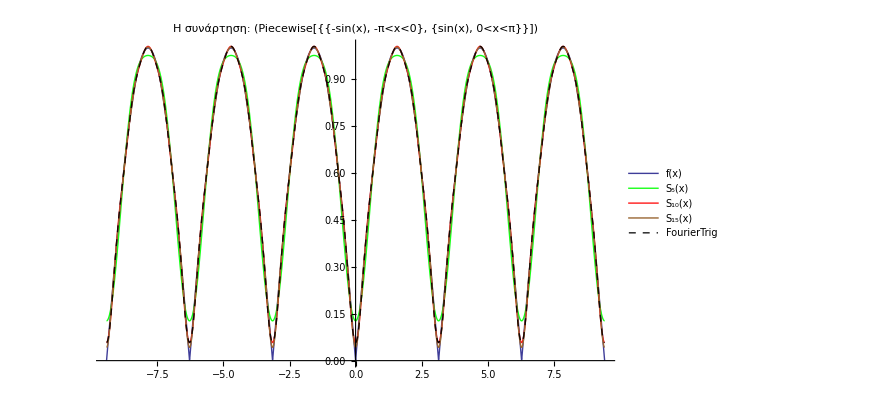

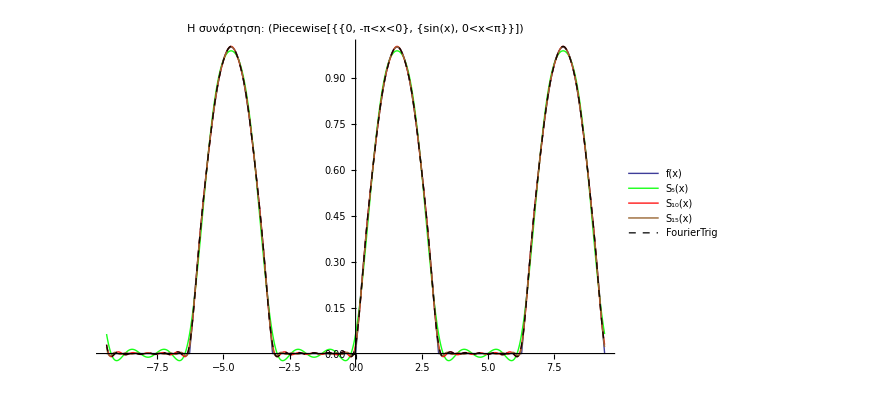

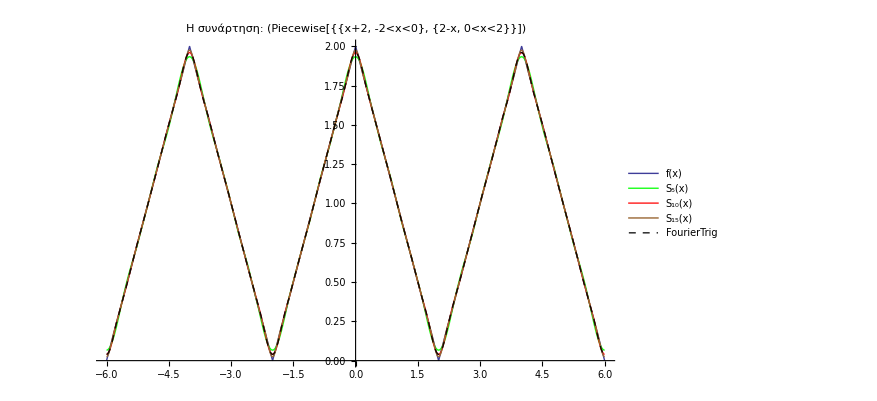

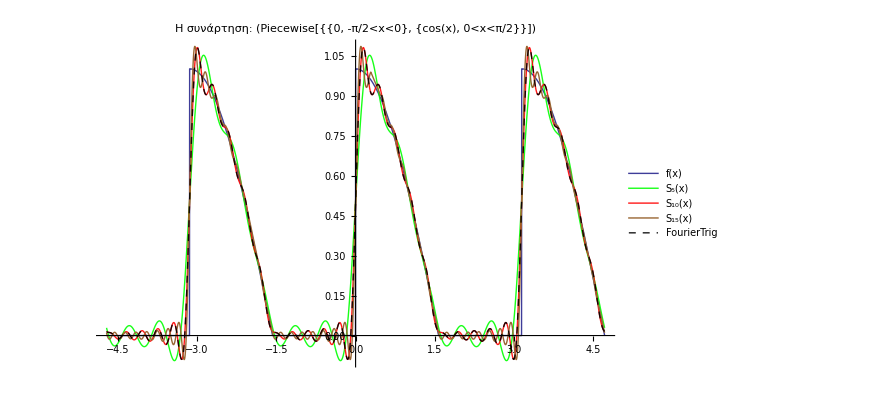

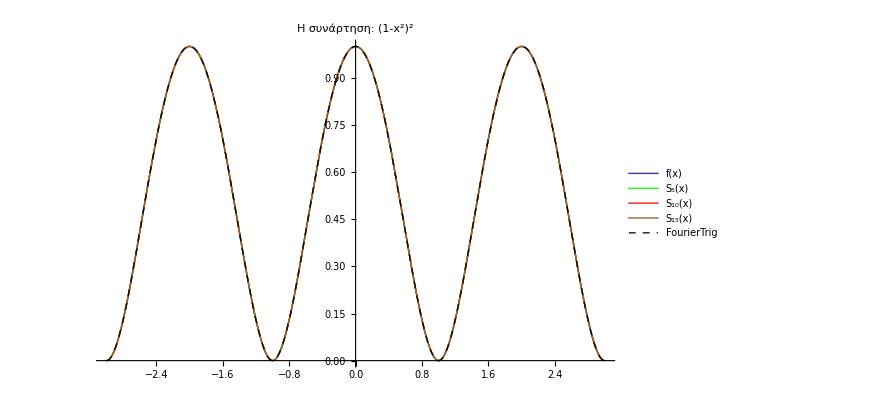

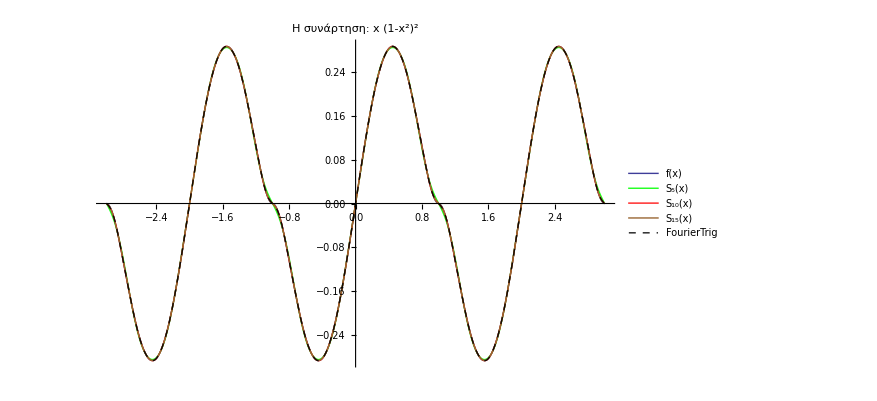

```mathematica
(*Ίσως πάρει ακρετό χρόνο για να τρέξει το πρόγραμμα! *)
Clear["Global`*"]

T[L_]:=2*L
(*Συνάρτηση που δίνει την περιοδική επέκταση της f*)
PeriodicExtension[f_,L_,x_]:=f[x-T[L]*IntegerPart[x/T[L]]-Sign[x]*T[L]*Mod[IntegerPart[x/L],2]]

(*Υπολογισμός των συντελεστών fourier*)
A0[f_,L_]:=1/L * Integrate[f[x],{x,-L,L}]
An[f_,n_,L_]:=1/L * Integrate[f[x]*Cos[n*Pi*x/L],{x,-L,L}]
Bn[f_,n_,L_]:=1/L * Integrate[f[x]*Sin[n*Pi*x/L],{x,-L,L}]

(*Ορισμός συνάρτησης Fourier*)
DefineFourier[f_,an_,bn_,L_,MaxI_]:=    A0[f,L]/2+Sum[ {an[i]*Cos[i*Pi*x/L]   +    bn[i]*Sin[i*Pi*x/L]  } , {i,1,MaxI}] 

(*Συνάρτηση που δίνει την γραφική παράσταση*)
PlotFourier[f_,L_,Fourier5_,Fourier10_,Fourier15_,FourierMathematica_]:=Plot[{PeriodicExtension[f,L,x],Fourier5[x],Fourier10[x],Fourier15[x],FourierMathematica[x]},{x,-3*L,3*L},PlotStyle->{{Thick},{Opacity[0.9],Green},{Opacity[0.9],Red},{Brown},{Dashed,Black,Opacity[0.9]}},PlotLegends->{"f(x)","S_5(x)","S_10(x)","S_15(x)","FourierTrig"},PlotRange->All,ImageSize->650,PlotLabel->Style["Η συνάρτηση: "f[x],FontSize->15]]


(*----------------α)------------*)
Fa[x_]=x^2;
(*  -La < x < La  *)
La:=1 
AnFa[n_]=An[Fa,n,La];    
BnFa[n_]=Bn[Fa,n,La];
(*ορίζουμε τις Συναρτήσεις fourier για n=5,10,15*)
FourierFa5[x_]=DefineFourier[Fa,AnFa,BnFa,La,5];
FourierFa10[x_]=DefineFourier[Fa,AnFa,BnFa,La,10];
FourierFa15[x_]=DefineFourier[Fa,AnFa,BnFa,La,15];

(*---------------------------ερώτημα β)-----------------------------------------*)
(*ορίζουμε την συνάρτηση fourier με την εντολή FourierTrigSeries για n=10 *)
(*Το Mathematica 9.0 έχει ως default διάστημα για την FourierTrigSeries το -π,π *)
(*άρα θα πρέπει να κάνουμε αλλαγή μεταβλητής x'=x/Pi *)
FourierMathematica[x_]=FourierTrigSeries[Fa[x/(Pi)],x,10];
FourierMathematica[x_]=FourierMathematica[x*Pi];

(*Τέλος παρουσιάζουμε όλες τις γραφικές παραστάσεις μαζί σε ένα γράφημα χρησιμοποιόντας την συνάρτηση που ορίσαμε παραπάνω*)
PlotFourier[Fa,La,FourierFa5,FourierFa10,FourierFa15,FourierMathematica]



(*Με παρόμοιο τρόπο ακολουθούν τα υπόλοιπα ερωτήματα της άσκησης του βιβλίου*)

(*----------------β)------------*)
Fb[x_]=Piecewise[{{1,-1<x<0},{0,0<x<1}}];
Lb:=1 
AnFb[n_]=An[Fb,n,Lb];    
BnFb[n_]=Bn[Fb,n,Lb];
FourierFb5[x_]=DefineFourier[Fb,AnFb,BnFb,Lb,5];
FourierFb10[x_]=DefineFourier[Fb,AnFb,BnFb,Lb,10];
FourierFb15[x_]=DefineFourier[Fb,AnFb,BnFb,Lb,15];
FourierMathematica[x_]=FourierTrigSeries[Fb[x/(Pi)],x,10];
FourierMathematica[x_]=FourierMathematica[x*Pi];
PlotFourier[Fb,Lb,FourierFb5,FourierFb10,FourierFb15,FourierMathematica]

(*----------------γ)------------*)
Fc[x_]=Piecewise[{{-Sin[x],-Pi<x<0},{Sin[x],0<x<Pi}}];
Lc:=Pi
AnFc[n_]=An[Fc,n,Lc];    
BnFc[n_]=Bn[Fc,n,Lc];
(*
Βρίσκουμε ότι An=-(2 (1+Cos[n π]))/((-1+n^2) π)  Bn=0 ;
Παρατηρούμε ότι για n=1 έχουμε πρόβλημα γιατί ο παρονομαστής μηδενίζεται.;
Οπότε υπολογίζουμε ξεχωριστά τo ολοκλήρωμα για n=1 και βρίσκουμε Α1=0 .;    
Τροποποιούμε την συνάρτηση DefineFourier και την αντικαθιστούμε με την παρακάτω συνάρτηση
*)
DefineFourierc[f_,an_,bn_,L_,MaxI_]:=    A0[f,L]/2   +Sum[ {an[i]*Cos[i*Pi*x/L]    } , {i,2,MaxI}] 
FourierFc5[x_]=DefineFourierc[Fc,AnFc,BnFc,Lc,5];
FourierFc10[x_]=DefineFourierc[Fc,AnFc,BnFc,Lc,10];
FourierFc15[x_]=DefineFourierc[Fc,AnFc,BnFc,Lc,15];
(*H FourierTrigSeries παρατηρούμε ότι έχει διπλάσια ακρίβεια από την συνάρτηση που φτιάξαμε*)
FourierMathematica[x_]=FourierTrigSeries[Fc[x/2],x,5];
FourierMathematica[x_]=FourierMathematica[x*2];
PlotFourier[Fc,Lc,FourierFc5,FourierFc10,FourierFc15,FourierMathematica]

(*----------------δ)------------*)
Fd[x_]=Piecewise[{{0,-Pi<x<0},{Sin[x],0<x<Pi}}];
Ld:=Pi
AnFd[n_]=An[Fd,n,Ld];
BnFd[n_]=Bn[Fd,n,Ld];
(*
Βρίσκουμε ότι An=(-1-Cos[n π])/((-1+n^2) π)  Bn=-Sin[n π]/((-1+n^2) π) ;
Παρατηρούμε ότι για n=1 έχουμε πρόβλημα γιατί ο παρονομαστής μηδενίζεται.;
Οπότε υπολογίζουμε ξεχωριστά τα ολοκληρώματα για n=1 και βρίσκουμε Α1=0 και Β1=1/2.;    
Τροποποιούμε την συνάρτηση DefineFourier και την αντικαθιστούμε με την παρακάτω συνάρτηση
*)
DefineFourierd[f_,an_,bn_,L_,MaxI_]:=    A0[f,L]/2 +   Sin[Pi*x/L] /2  +Sum[ {an[i]*Cos[i*Pi*x/L]   +    bn[i]*Sin[i*Pi*x/L]  } , {i,2,MaxI}] 
FourierFd5[x_]=DefineFourierd[Fd,AnFd,BnFd,Ld,5];
FourierFd10[x_]=DefineFourierd[Fd,AnFd,BnFd,Ld,10];
FourierFd15[x_]=DefineFourierd[Fd,AnFd,BnFd,Ld,15];
FourierMathematica[x_]=FourierTrigSeries[Fd[x],x,10];
FourierMathematica[x_]=FourierMathematica[x];
PlotFourier[Fd,Ld,FourierFd5,FourierFd10,FourierFd15,FourierMathematica]

(*----------------ε)------------*)
Fe[x_]=Piecewise[{{x+2,-2<x<0},{2-x,0<x<2}}];
Le:=2
AnFe[n_]=An[Fe,n,Le];
BnFe[n_]=Bn[Fe,n,Le];
FourierFe5[x_]=DefineFourier[Fe,AnFe,BnFe,Le,5];
FourierFe10[x_]=DefineFourier[Fe,AnFe,BnFe,Le,10];
FourierFe15[x_]=DefineFourier[Fe,AnFe,BnFe,Le,15];
FourierMathematica[x_]=FourierTrigSeries[Fe[x*2/(Pi)],x,10];
FourierMathematica[x_]=FourierMathematica[x*(Pi)/2];
PlotFourier[Fe,Le,FourierFe5,FourierFe10,FourierFe15,FourierMathematica]

(*----------------στ)------------*)
Fst[x_]=Piecewise[{{0,-Pi/2<x<0},{Cos[x],0<x<Pi/2}}];
Lst:=Pi/2
AnFst[n_]=An[Fst,n,Lst];
BnFst[n_]=Bn[Fst,n,Lst];
FourierFst5[x_]=DefineFourier[Fst,AnFst,BnFst,Lst,5];
FourierFst10[x_]=DefineFourier[Fst,AnFst,BnFst,Lst,10];
FourierFst15[x_]=DefineFourier[Fst,AnFst,BnFst,Lst,15];
FourierMathematica[x_]=FourierTrigSeries[Fst[x/2],x,10];
FourierMathematica[x_]=FourierMathematica[x*2];
PlotFourier[Fst,Lst,FourierFst5,FourierFst10,FourierFst15,FourierMathematica]

(*----------------ζ)------------*)
Fz[x_]=(1-x^2)^2;
Lz:=1
AnFz[n_]=An[Fz,n,Lz];
BnFz[n_]=Bn[Fz,n,Lz];
FourierFz5[x_]=DefineFourier[Fz,AnFz,BnFz,Lz,5];
FourierFz10[x_]=DefineFourier[Fz,AnFz,BnFz,Lz,10];
FourierFz15[x_]=DefineFourier[Fz,AnFz,BnFz,Lz,15];
FourierMathematica[x_]=FourierTrigSeries[Fz[x/(Pi)],x,10];
FourierMathematica[x_]=FourierMathematica[x*(Pi)];
PlotFourier[Fz,Lz,FourierFz5,FourierFz10,FourierFz15,FourierMathematica]

(*----------------η)------------*)
Fh[x_]=x*(1-x^2)^2;
Lh:=1
AnFh[n_]=An[Fh,n,Lh];
BnFh[n_]=Bn[Fh,n,Lh];
FourierFh5[x_]=DefineFourier[Fh,AnFh,BnFh,Lh,5];
FourierFh10[x_]=DefineFourier[Fh,AnFh,BnFh,Lh,10];
FourierFh15[x_]=DefineFourier[Fh,AnFh,BnFh,Lh,15];
FourierMathematica[x_]=FourierTrigSeries[Fh[x/(Pi)],x,10];
FourierMathematica[x_]=FourierMathematica[x*(Pi)];
PlotFourier[Fh,Lh,FourierFh5,FourierFh10,FourierFh15,FourierMathematica]
```

Ασκηση 2

Τα αποτελέσματα της άσκησης 2 επιβαιβεώνουν οι γραφικές παραστάσεις τις άσκησης 1.
Παρατηρούμε ότι το σφάλμα στα άκρα του διαστήματος τείνει να γίνεται μεγαλύτερο.
Επίσης όπως ήταν ανεμενόμενο στις περισσότερες περιπτώσεις η Euler-15 
παρουσιάζει μικρότερο σφάλμα από τις υπόλοιπες δύο , και η Euler-10 παρουσιάζει 
μικρότερο σφάλμα από την Euler-5.
Αυτό δεν συμβαίνει πάντα γιατί τα σημεία που επιλέγουμε είναι τυχαία και σε ορισμένες
περιπτώσεις η  Euler-5 έχει καλύτερο σφάλμα ακόμα και από την Euler-15 !

```mathematica
(*-----------------------!!!!!!!!!!!!!!!!!---------------------*)
(* Για να τρέξει η άσκηση 2 πρέπει πρώτα  να τρέξει η άσκηση 1 *)

(*Συνάρτηση που υπολογίζει την απόσταση δύο αριθμών*)
Error[a_,b_]:=N[Abs[a-b],7]

(*Συνάρτηση που παρουσιάζει τα αποτελέσματα μέσω TableForm*)
(*Δέχεται σαν όρισμα συναρτήσεις που υπολογίζουν το σφάλμα μεταξύ της Euler5-10-15 και της αντίστοιχης f(x) για οποιοδήποτε χ *)
(*Στις συναρτήσεις Error5-10-15 δίνουμε ως x τα σημεία της διαμέρισης*)
TableFormFunction[Error5_,Error10_,Error15_]:=TableForm[ Table[{SimioDiamerisis[x],Error5[SimioDiamerisis[x]],Error10[SimioDiamerisis[x]],Error15[SimioDiamerisis[x]]},{x,1,10}] 
,TableSpacing->{4,4},TableAlignments->Center,TableHeadings->{ None,{"x", "  |f(x)-SCell["5"](x)|", " |f(x)-SCell["10"](x)|", "  |f(x)-SCell["15"](x)|"}} ]

(*συνάρτηση που υπολογίζει τα σημεία της διαμέρισης με δεδομένο i*)
(*Το διάστημα ( (-L+0.001) , (L-0.001) ) χωρίζεται σε 10 ίσα υποδιαστήματα*)
SimioDiamerisis[i_]:=(-L+0.001+(i-1)*(2L-0.002)/9)
(*Αν θέλουμε να αλλάξουμε τα σημεία της διαμέρισης τροποποιούμε αυτή τη συνάρτηση *)
(*π.χ. SimioDiamerisis[i_]:=(-L+(i-1)*(2L)/9) *)


(*--------------------------Για την α) συνάρτηση------------------------------------*)

(*ορίζουμε ως L το La (ορίστηκε από την άσκηση 1) ,αναλόγως για τις υπόλοιπες συναρτήσεις*)
L=La;
(*ορίζουμε τις συναρτήσεις που δίνουν το σφάλμα μεταξύ Euler5-10-15 και  f(x) σε κάθε σημείο*)
ErrorFa5[x_]:= Error[FourierFa5[x][[1]],Fa[x]]
ErrorFa10[x_]:= Error[FourierFa10[x][[1]],Fa[x]]
ErrorFa15[x_]:= Error[FourierFa15[x][[1]],Fa[x]]

Print["α)  Για την συνάρτηση: ",Fa[x],"  ,βρίσκουμε τα παρακάτω αποτελέσματα"]
TableFormFunction[ErrorFa5,ErrorFa10,ErrorFa15]


(*------------Για τις υπόλοιπες συναρτήσεις ακολουθούμε τα ίδια βήματα----------------*)
 
L=Lb;
ErrorFb5[x_]:= Error[FourierFb5[x][[1]],Fb[x]]
ErrorFb10[x_]:= Error[FourierFb10[x][[1]],Fb[x]]
ErrorFb15[x_]:= Error[FourierFb15[x][[1]],Fb[x]]
Print["\nβ)  Για την συνάρτηση: ",Fb[x],"  ,βρίσκουμε τα παρακάτω αποτελέσματα"]
TableFormFunction[ErrorFb5,ErrorFb10,ErrorFb15]


L=Lc;
ErrorFc5[x_]:= Error[FourierFc5[x][[1]],Fc[x]]
ErrorFc10[x_]:= Error[FourierFc10[x][[1]],Fc[x]]
ErrorFc15[x_]:= Error[FourierFc15[x][[1]],Fc[x]]
Print["\nγ)  Για την συνάρτηση: ",Fc[x],"  ,βρίσκουμε τα παρακάτω αποτελέσματα"]
TableFormFunction[ErrorFc5,ErrorFc10,ErrorFc15]

L=Ld;
ErrorFd5[x_]:= Error[FourierFd5[x][[1]],Fd[x]]
ErrorFd10[x_]:= Error[FourierFd10[x][[1]],Fd[x]]
ErrorFd15[x_]:= Error[FourierFd15[x][[1]],Fd[x]]
Print["\nδ)  Για την συνάρτηση: ",Fd[x],"  ,βρίσκουμε τα παρακάτω αποτελέσματα"]
TableFormFunction[ErrorFd5,ErrorFd10,ErrorFd15]

L=Le;
ErrorFe5[x_]:= Error[FourierFe5[x][[1]],Fe[x]]
ErrorFe10[x_]:= Error[FourierFe10[x][[1]],Fe[x]]
ErrorFe15[x_]:= Error[FourierFe15[x][[1]],Fe[x]]
Print["\nε)  Για την συνάρτηση: ",Fd[x],"  ,βρίσκουμε τα παρακάτω αποτελέσματα"]
TableFormFunction[ErrorFe5,ErrorFe10,ErrorFe15]

L=Lst;
ErrorFst5[x_]:= Error[FourierFst5[x][[1]],Fst[x]]
ErrorFst10[x_]:= Error[FourierFst10[x][[1]],Fst[x]]
ErrorFst15[x_]:= Error[FourierFst15[x][[1]],Fst[x]]
Print["\nστ)  Για την συνάρτηση: ",Fst[x],"  ,βρίσκουμε τα παρακάτω αποτελέσματα"]
TableFormFunction[ErrorFst5,ErrorFst10,ErrorFst15]

L=Lz;
ErrorFz5[x_]:= Error[FourierFz5[x][[1]],Fz[x]]
ErrorFz10[x_]:= Error[FourierFz10[x][[1]],Fz[x]]
ErrorFz15[x_]:= Error[FourierFz15[x][[1]],Fz[x]]
Print["\nζ)  Για την συνάρτηση: ",Fz[x],"  ,βρίσκουμε τα παρακάτω αποτελέσματα"]
TableFormFunction[ErrorFz5,ErrorFz10,ErrorFz15]

L=Lh;
ErrorFh5[x_]:= Error[FourierFh5[x][[1]],Fh[x]]
ErrorFh10[x_]:= Error[FourierFh10[x][[1]],Fh[x]]
ErrorFh15[x_]:= Error[FourierFh15[x][[1]],Fh[x]]
Print["\nη)  Για την συνάρτηση: ",Fh[x],"  ,βρίσκουμε τα παρακάτω αποτελέσματα"]
TableFormFunction[ErrorFh5,ErrorFh10,ErrorFh15]
```

α)  Για την συνάρτηση: x^2  ,βρίσκουμε τα παρακάτω αποτελέσματα

x |   |f(x)-SCell["5"](x)| |  |f(x)-SCell["10"](x)| |   |f(x)-SCell["15"](x)|
-0.999 | 0.0714984 | 0.0365905 | 0.0241693
-0.777 | 0.00531278 | 0.00374923 | 0.00227513
-0.555 | 0.00919067 | 0.00254627 | 0.000502993
-0.333 | 0.00679976 | 0.0000899631 | 0.000829301
-0.111 | 0.00244682 | 0.00159302 | 0.000552572
0.111 | 0.00244682 | 0.00159302 | 0.000552572
0.333 | 0.00679976 | 0.0000899631 | 0.000829301
0.555 | 0.00919067 | 0.00254627 | 0.000502993
0.777 | 0.00531278 | 0.00374923 | 0.00227513
0.999 | 0.0714984 | 0.0365905 | 0.0241693

β)  Για την συνάρτηση: Piecewise[{{1, -1<x<0}, {0, True}}]  ,βρίσκουμε τα παρακάτω αποτελέσματα

x |   |f(x)-SCell["5"](x)| |  |f(x)-SCell["10"](x)| |   |f(x)-SCell["15"](x)|
-0.999 | 0.494 | 0.490001 | 0.484002
-0.777 | 0.0483895 | 0.0393359 | 0.00432026
-0.555 | 0.025501 | 0.00553491 | 0.0187802
-0.333 | 0.0589357 | 0.0201568 | 0.0124453
-0.111 | 0.0266211 | 0.0854721 | 0.036612
0.111 | 0.0266211 | 0.0854721 | 0.036612
0.333 | 0.0589357 | 0.0201568 | 0.0124453
0.555 | 0.025501 | 0.00553491 | 0.0187802
0.777 | 0.0483895 | 0.0393359 | 0.00432026
0.999 | 0.494 | 0.490001 | 0.484002

γ)  Για την συνάρτηση: Piecewise[{{-Sin[x], -π<x<0}, {Sin[x], 0<x<π}, {0, True}}]  ,βρίσκουμε τα παρακάτω αποτελέσματα

x |   |f(x)-SCell["5"](x)| |  |f(x)-SCell["10"](x)| |   |f(x)-SCell["15"](x)|
-3.14059 | 0.126325 | 0.056878 | 0.0414461
-2.44268 | 0.0000417478 | 0.00726625 | 0.00336839
-1.74477 | 0.0144503 | 0.001917 | 0.00248566
-1.04686 | 0.0252619 | 0.00540965 | 0.000255762
-0.348955 | 0.0452528 | 0.00399078 | 0.00732912
0.348955 | 0.0452528 | 0.00399078 | 0.00732912
1.04686 | 0.0252619 | 0.00540965 | 0.000255762
1.74477 | 0.0144503 | 0.001917 | 0.00248566
2.44268 | 0.0000417478 | 0.00726625 | 0.00336839
3.14059 | 0.126325 | 0.056878 | 0.0414461

δ)  Για την συνάρτηση: Piecewise[{{0, -π<x<0}, {Sin[x], 0<x<π}, {0, True}}]  ,βρίσκουμε τα παρακάτω αποτελέσματα

x |   |f(x)-SCell["5"](x)| |  |f(x)-SCell["10"](x)| |   |f(x)-SCell["15"](x)|
-3.14059 | 0.0631627 | 0.028439 | 0.020723
-2.44268 | 0.0000208739 | 0.00363312 | 0.0016842
-1.74477 | 0.00722514 | 0.000958502 | 0.00124283
-1.04686 | 0.0126309 | 0.00270482 | 0.000127881
-0.348955 | 0.0226264 | 0.00199539 | 0.00366456
0.348955 | 0.0226264 | 0.00199539 | 0.00366456
1.04686 | 0.0126309 | 0.00270482 | 0.000127881
1.74477 | 0.00722514 | 0.000958502 | 0.00124283
2.44268 | 0.0000208739 | 0.00363312 | 0.0016842
3.14059 | 0.0631627 | 0.028439 | 0.020723

ε)  Για την συνάρτηση: Piecewise[{{0, -π<x<0}, {Sin[x], 0<x<π}, {0, True}}]  ,βρίσκουμε τα παρακάτω αποτελέσματα

x |   |f(x)-SCell["5"](x)| |  |f(x)-SCell["10"](x)| |   |f(x)-SCell["15"](x)|
-1.999 | 0.0659475 | 0.0394002 | 0.0243055
-1.55478 | 0.0101989 | 0.00281927 | 0.00238253
-1.11056 | 0.00942052 | 0.00391748 | 0.000532205
-0.666333 | 0.00193977 | 0.00362313 | 0.0014832
-0.222111 | 0.0233158 | 0.00064971 | 0.00354071
0.222111 | 0.0233158 | 0.00064971 | 0.00354071
0.666333 | 0.00193977 | 0.00362313 | 0.0014832
1.11056 | 0.00942052 | 0.00391748 | 0.000532205
1.55478 | 0.0101989 | 0.00281927 | 0.00238253
1.999 | 0.0659475 | 0.0394002 | 0.0243055

στ)  Για την συνάρτηση: Piecewise[{{0, -π/2<x<0}, {Cos[x], 0<x<π/2}, {0, True}}]  ,βρίσκουμε τα παρακάτω αποτελέσματα

x |   |f(x)-SCell["5"](x)| |  |f(x)-SCell["10"](x)| |   |f(x)-SCell["15"](x)|
-1.5698 | 0.0281181 | 0.01498 | 0.0094544
-1.22095 | 0.0227783 | 0.0127667 | 0.0117143
-0.872109 | 0.0409627 | 0.0155705 | 0.00422365
-0.523265 | 0.046726 | 0.00265292 | 0.018671
-0.174422 | 0.000109154 | 0.0771987 | 0.0289556
0.174422 | 0.00183227 | 0.0784517 | 0.0285201
0.523265 | 0.0413365 | 0.00257527 | 0.0180213
0.872109 | 0.0337017 | 0.0175818 | 0.0038187
1.22095 | 0.0186629 | 0.0156937 | 0.00993169
1.5698 | 0.0287599 | 0.0143419 | 0.0100916

ζ)  Για την συνάρτηση: (1-x^2)^2  ,βρίσκουμε τα παρακάτω αποτελέσματα

x |   |f(x)-SCell["5"](x)| |  |f(x)-SCell["10"](x)| |   |f(x)-SCell["15"](x)|
-0.999 | 0.000970957 | 0.000141024 | 0.0000438645
-0.777 | 0.0000294241 | 0.0000301059 | 0.0000102658
-0.555 | 0.000308403 | 0.0000282169 | 2.9273×10^-6
-0.333 | 0.000264899 | 2.13894×10^-6 | 4.06272×10^-6
-0.111 | 0.0000995921 | 0.0000171253 | 2.81188×10^-6
0.111 | 0.0000995921 | 0.0000171253 | 2.81188×10^-6
0.333 | 0.000264899 | 2.13894×10^-6 | 4.06272×10^-6
0.555 | 0.000308403 | 0.0000282169 | 2.9273×10^-6
0.777 | 0.0000294241 | 0.0000301059 | 0.0000102658
0.999 | 0.000970957 | 0.000141024 | 0.0000438645

η)  Για την συνάρτηση: x (1-x^2)^2  ,βρίσκουμε τα παρακάτω αποτελέσματα

x |   |f(x)-SCell["5"](x)| |  |f(x)-SCell["10"](x)| |   |f(x)-SCell["15"](x)|
-0.999 | 0.000285108 | 0.0001496 | 0.000100375
-0.777 | 0.00326741 | 0.000428095 | 0.0000706445
-0.555 | 0.000877468 | 0.000123083 | 0.000095511
-0.333 | 0.000610643 | 0.000248596 | 0.0000419981
-0.111 | 0.00132301 | 0.000114018 | 0.0000527016
0.111 | 0.00132301 | 0.000114018 | 0.0000527016
0.333 | 0.000610643 | 0.000248596 | 0.0000419981
0.555 | 0.000877468 | 0.000123083 | 0.000095511
0.777 | 0.00326741 | 0.000428095 | 0.0000706445
0.999 | 0.000285108 | 0.0001496 | 0.000100375

Ασκηση 3

α) ερώτημα - άσκηση 1 σελ. 263

α) H διαφορική εξίσωση y'= sin(xy) ,y(0)=1

• Λύση απλής Euler        : 0.317400444757586
• Λύση βελτιωμένης Euler  : 0.317400795150958
• Λύση NDSolve            : 0.31740079385204

Παρατηρούμε ότι η λύση με την μέθοδο της βελτιωμένης Euler είναι πιο κοντά στην λύση της NDSolve.
Η γραφική παράσταση της λύσης:

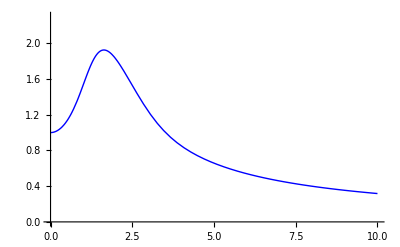

β) Η διαφορική y'=x^2-y^2 ,y(0)=-1

• Λύση απλής Euler        : -5.91482475144859482979922
• Λύση βελτιωμένης Euler  : -5.91482470355743903803023
• Λύση NDSolve            : -5.91482470358579429968771

Παρατηρούμε ότι η λύση με την μέθοδο της βελτιωμένης Euler είναι πιο κοντά στην λύση της NDSolve.
Η γραφική παράσταση της λύσης:

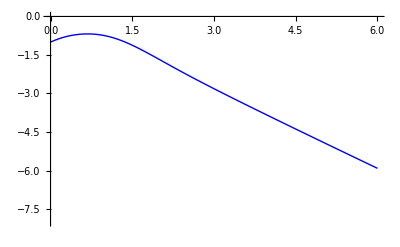

```mathematica
(* ----------------------α) η διαφορική y'= sin(xy) ,y(0)=1 --------------------------------------  *)
Clear["Global`*"]

DigitsPrecision:=15
NumberOfPoints:=10000
h:=N[1/1000,DigitsPrecision+22]
MaxLength:=NumberOfPoints*h

f[x_,y_]:=Sin[x y]

P[q_]:=(u[0]=1; Do[u[n+1]=  u[n]+h*   f[n*h+(h*q/2),u[n]+(h*q/2)*f[n*h,u[n]]],{n,0,NumberOfPoints}]);

(*για q=0 έχουμε την απλή μέθοδο του Euler*)
P[0]
EulerClassic=u[NumberOfPoints];

(*για q=1 έχουμε την σύνθετη μέθοδο του Euler*)
P[1]
EulerUpgrade=u[NumberOfPoints];

s=NDSolve[{y'[x]==Sin[x*y[x]],y[0]==1},y,{x,0,MaxLength},WorkingPrecision->DigitsPrecision,PrecisionGoal->DigitsPrecision];
NDSolveF=(y[MaxLength]/.s)[[1]];

Print["α) H διαφορική εξίσωση y'= sin(xy) ,y(0)=1\n\n• Λύση απλής Euler        : ",Style[EulerClassic,FontColor->Red],
"\n• Λύση βελτιωμένης Euler  : ",Style[EulerUpgrade,FontColor->Blue],
"\n• Λύση NDSolve            : ",NDSolveF,
"\n\nΠαρατηρούμε ότι η λύση με την μέθοδο της βελτιωμένης Euler είναι πιο κοντά στην λύση της NDSolve.\nΗ γραφική παράσταση της λύσης:"]

InterpolationEulerF=Interpolation[Table[{h*n,u[n]},{n,0,NumberOfPoints}]];
Plot[InterpolationEulerF[t],{t,0,MaxLength},PlotRange->{0,2.3},PlotStyle->{Blue}]



(*  ------------------- β) η διαφορική y'= x^2-y^2 ,y(0)=-1 -------------------------   *)
Clear["Global`*"]

DigitsPrecision:=25
NumberOfPoints:=30000
h:=N[1/5000,39]
MaxLength:=NumberOfPoints*h

f[x_,y_]:=y^2-x^2

P[q_]:=(u[0]=-1; Do[u[n+1]=  u[n]+h*   f[n*h+(h*q/2),u[n]+(h*q/2)*f[n*h,u[n]]],{n,0,NumberOfPoints}]);

P[0]
EulerClassic=u[NumberOfPoints];

P[1]
EulerUpgrade=u[NumberOfPoints];

s=NDSolve[{y'[x]==y[x]^2-x^2,y[0]==-1},y,{x,0,MaxLength},WorkingPrecision->DigitsPrecision,PrecisionGoal->DigitsPrecision];
NDSolveF=(y[MaxLength]/.s)[[1]];

Print["\nβ) Η διαφορική y'=x^2-y^2 ,y(0)=-1\n\n• Λύση απλής Euler        : ",Style[EulerClassic,FontColor->Red],
"\n• Λύση βελτιωμένης Euler  : ",Style[EulerUpgrade,FontColor->Blue],
"\n• Λύση NDSolve            : ",NDSolveF,
"\n\nΠαρατηρούμε ότι η λύση με την μέθοδο της βελτιωμένης Euler είναι πιο κοντά στην λύση της NDSolve.\nΗ γραφική παράσταση της λύσης:"]

InterpolationEulerF=Interpolation[Table[{h*n,u[n]},{n,0,NumberOfPoints}]];
Plot[InterpolationEulerF[t],{t,0,MaxLength},PlotRange->{-8,0},PlotStyle->{Blue}]
```

β) ερώτημα - άσκηση 3 σελ. 264

α) H διαφορική  y'' + 4y' + 3y = 0 
   H τιμή y(5.5) :
   Με το πρόγραμμα S : 0.00409181
   Με την NDSolve    : 0.0040867

Οι γραφικές παραστάσεις των δύο μεθόδων:

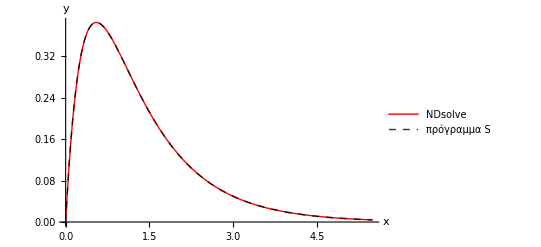

β) H διαφορική  y'' + xy = 0 
   H τιμή y(16.) :
   Με το πρόγραμμα S : -0.00376955
   Με την NDSolve    : -0.00378987

Οι γραφικές παραστάσεις των δύο μεθόδων:

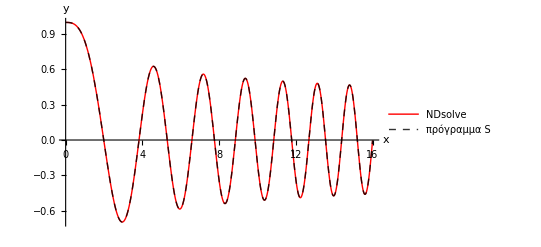

```mathematica
Clear["Global`*"]

(*---------------------------------------------α) ερώτημα------------------------------------------------ *)
NumberOfPoints:=11000
h:=0.0005
MaxLength:=NumberOfPoints*h

f[x_,y_,z_]:=-3y-4z

S[a_,b_,h_,N_]:=(u[0]=a;u[1]=a+h*b; Do[u[n+1]=2u[n]-u[n-1]+h*h*f[n*h,u[n],(u[n]-u[n-1])/h],{n,1,N}])

p=NDSolve[{y''[x]+4y'[x]+3y[x]==0,y[0]==0,y'[0]==2},y,{x,0,MaxLength}];

S[0,2,h,NumberOfPoints];

InterpolationS=Interpolation[Table[{h*n,u[n]},{n,0,NumberOfPoints}]];

temp=y[MaxLength]/.p;
Print["α) H διαφορική  y'' + 4y' + 3y = 0 \n   H τιμή y(",MaxLength,") :\n   Με το πρόγραμμα S : ",InterpolationS[MaxLength],"\n   Με την NDSolve    : ",temp[[1]],"\n\nΟι γραφικές παραστάσεις των δύο μεθόδων:"]

Plot[{Evaluate[y[t]/.p],InterpolationS[t]},{t,0,MaxLength},PlotStyle->{{Red},{Black,Opacity[0.8],Dashed}},PlotRange->All,PlotLegends->{"NDsolve","πρόγραμμα S"},AxesOrigin->{0,0},AxesLabel->{"x","y"}]



(*--------------------------------------------β) ερώτημα--------------------------------------------- *)
NumberOfPoints:=10000
h:=0.0016
MaxLength:=NumberOfPoints*h

g[x_,y_,z_]:=-x*y

S2[a_,b_,h_,N_]:=(u[0]=a;u[1]=a+h*b; Do[u[n+1]=2u[n]-u[n-1]+h*h*g[n*h,u[n],(u[n]-u[n-1])/h],{n,1,N}])

p=NDSolve[{y''[x]+x*y[x]==0,y[0]==1,y'[0]==0},y,{x,0,MaxLength}];

S2[1,0,h,NumberOfPoints];

InterpolationS=Interpolation[Table[{h*n,u[n]},{n,0,NumberOfPoints}]];

temp=y[MaxLength]/.p;
Print["\nβ) H διαφορική  y'' + xy = 0 \n   H τιμή y(",MaxLength,") :\n   Με το πρόγραμμα S : ",InterpolationS[MaxLength],"\n   Με την NDSolve    : ",temp[[1]],"\n\nΟι γραφικές παραστάσεις των δύο μεθόδων:"]

Plot[{Evaluate[y[t]/.p],InterpolationS[t]},{t,0,MaxLength},PlotStyle->{{Red},{Black,Opacity[0.8],Dashed}},PlotRange->All,PlotLegends->{"NDsolve","πρόγραμμα S"},AxesOrigin->{0,0},AxesLabel->{"x","y"}]
```

Ασκηση 4

Αριθμητική επίλυση - Γραφικές παραστάσεις

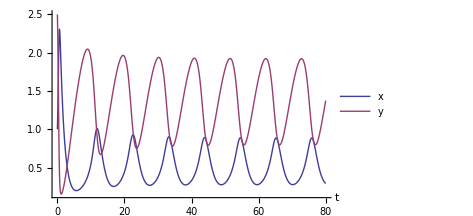
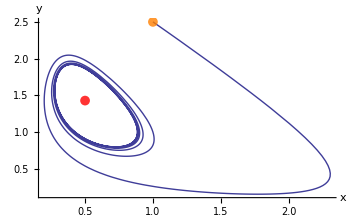
Ερώτημα α)
i) Οι γραφικές παραστάσεις για  Α=0.1 , Β=0.5  και  x(0)=1 , y(0)=2.5 :
  -Graphics- | -Graphics-

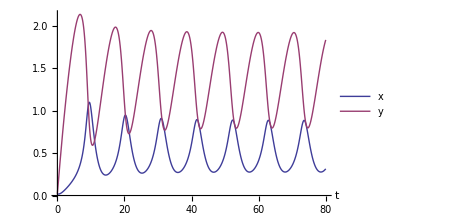
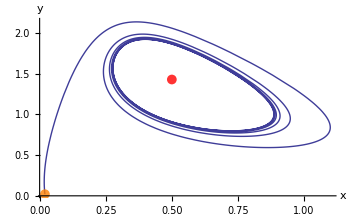
ii) Οι γραφικές παραστάσεις για  Α=0.1 , Β=0.5  και  x(0)=0.02 , y(0)=0.02 :
  -Graphics- | -Graphics-

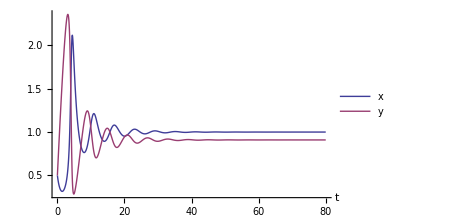
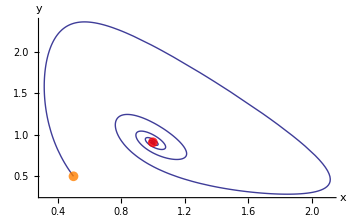
Ερώτημα β)
Οι γραφικές παραστάσεις για  Α=0.1 , Β=1  και  x(0)=0.5 , y(0)=0.5 :
  -Graphics- | -Graphics-

```mathematica
Clear["Global`*"]

Q[x0_,y0_,h_,N_]:=(u[0]=x0;v[0]=y0;Do[{u[n+1]=u[n]+h F[u[n]+h/2 F[u[n],v[n]],v[n]+h/2 G[u[n],v[n]]],v[n+1]=v[n]+h G[u[n]+h/2 F[u[n],v[n]],v[n]+h/2 G[u[n],v[n]]]},{n,0,N}])

PlotFunction[X_,Y_,tmax_]:=Plot[{X[x],Y[x]},{x,0,tmax},AxesLabel->{"t",None},PlotLegends->{"x","y"},PlotRange->All,AxesOrigin->{0,0},AspectRatio->1/GoldenRatio,ImageSize->{350,350}]

ParametricPlotFunction[X_,Y_,tmax_]:=ParametricPlot[{X[t],Y[t]},{t,0,tmax},Epilog->{{Red,PointSize[0.02],Opacity[0.8],Point[{B,B/(A+B^2)}]},{PointSize[0.02],Orange,Opacity[0.8],Point[{x0,y0}]}},PlotRange->All,AspectRatio->1/GoldenRatio,AxesOrigin->{0,0},AxesLabel->{"x","y"},ImageSize->{350,350}]


F[x_,y_]=-x+A*y+x^2* y;
G[x_,y_]=B-A*y-x^2*y;

n:=8010
h:=0.01
length:=((n-10)*h)

(* ------------------------- ερώτημα α)  i)  ------------------------------------  *)
A=0.1;
B=0.5;
x0=1;
y0=2.5;
Q[x0,y0,h,n];
X=Interpolation[Table[{h*i,u[i]},{i,0,n}]];
Y=Interpolation[Table[{h*i,v[i]},{i,0,n}]];

Print["Ερώτημα α)\ni) Οι γραφικές παραστάσεις για  Α=",A," , Β=",B,"  και  x(0)=",x0," , y(0)=",y0," :\n  ",Grid[{{PlotFunction[X,Y,length],ParametricPlotFunction[X,Y,length]}},ItemSize->{{34,37}}]]


(* --------------------------ερώτημα α)  ii)  ----------------------------------  *)
x0=0.02;
y0=0.02;
Q[x0,y0,h,n];
X=Interpolation[Table[{h*i,u[i]},{i,0,n}]];
Y=Interpolation[Table[{h*i,v[i]},{i,0,n}]];

Print["\nii) Οι γραφικές παραστάσεις για  Α=",A," , Β=",B,"  και  x(0)=",x0," , y(0)=",y0," :\n  ",Grid[{{PlotFunction[X,Y,length],ParametricPlotFunction[X,Y,length]}},ItemSize->{{34,37}}]]

(*  -------------------------ερώτημα β) ----------------------------------------   *)
B=1;
x0=0.5;
y0=0.5;
Q[x0,y0,h,n];
X=Interpolation[Table[{h*i,u[i]},{i,0,n}]];
Y=Interpolation[Table[{h*i,v[i]},{i,0,n}]];

Print["Ερώτημα β)\nΟι γραφικές παραστάσεις για  Α=",A," , Β=",B,"  και  x(0)=",x0," , y(0)=",y0," :\n  ",Grid[{{PlotFunction[X,Y,length],ParametricPlotFunction[X,Y,length]}},ItemSize->{{34,37}}]]


(* H γραφική παράσταση με Manipulate των τιμών Α,Β,χ0,y0 

n=500;
h=0.1;
ParametricPlotFunction2[X_,Y_,tmax_,Aa_,Bb_,x0_,y0_]:=ParametricPlot[{X[t],Y[t]},{t,0,tmax},Epilog->{{Red,PointSize[0.02],Opacity[0.8],Point[{Bb,Bb/(Aa+Bb^2)}]},{PointSize[0.02],Orange,Opacity[0.8],Point[{x0,y0}]}},PlotRange->All,AspectRatio->1/GoldenRatio,AxesOrigin->{0,0},AxesLabel->{"x","y"},ImageSize->{350,350}]

Manipulate[
F[x_,y_]=-x+A*y+x^2* y;
G[x_,y_]=B-A*y-x^2*y;
Q[x0,y0,h,n];
X=Interpolation[Table[{h*i,u[i]},{i,0,n}]];
Y=Interpolation[Table[{h*i,v[i]},{i,0,n}]];
ParametricPlotFunction2[X,Y,length,A,B,x0,y0],{A,0.05,0.5,0.01,Appearance->"Labeled"},{B,0.3,1.2,0.01,Appearance->"Labeled"},{x0,0.1,2,0.1,Appearance->"Labeled"},{y0,0.1,2,0.1,Appearance->"Labeled"}]
*)
```

Συμπεράσματα - Σημείο ισορροπίας

Παρατηρούμε ότι στην περίπτωση α) οι τροχιές μετά από κάποιο χρόνο προσεγγίζουν έναν κύκλο γύρο από το κρίσημο σημείο.
Ενώ στην περίπτωση β) οι τροχιές συγκλίνουν στο κρίσημο σημείο.
Το φαινόμενο της περίπτωσης α) συμβαίνει όταν το σημείο είναι ασταθές
Το φαινόμενο της περίπτωσης β) συμβαίνει όταν το σημείο είναι ευσταθές
Για την ευστάθεια του σημείου ορίζουμε τον παρακάτω πίνακα J. 
Όταν οι ιδιοτιμές είναι θετικές (ή με θετικό πραγματικό μέλος όταν είναι μιγαδικές) το σημείο είναι ασταθές, όπως στην περίπτωση α).
Όταν οι ιδιοτιμές είναι αρνητικές (ή με αρνητικό πραγματικό μέλος όταν είναι μιγαδικές) το σημείο είναι ευσταθές, όπως στην περίπτωση β).
Τέλος στην περίπτωση που οι ιδιοτιμές είναι καθαρά φανταστικοί αριθμοί, έχουμε ασυμπτωτική ευστάθεια.

```mathematica
Clear["Global`*"]
FAB[x_,y_,A_]=-x+A*y+x^2*y;
GAB[x_,y_,B_]=B-A*y-x^2*y;

p=Solve[FAB[x,y,A]==0&&GAB[x,y,B]==0,{x,y}];

Print["Το σημείο ισορροπίας είναι:",p[[1]]]

J=MatrixForm[JM[x_,y_,A_,B_]={{D[FAB[x,y,A], x],D[FAB[x,y,A], y]},{D[GAB[x,y,B], x],D[GAB[x,y,B], y]}}];
idiotimes=FullSimplify[Eigenvalues[JM[B,(B/(A+B^2)),A,B]]];

Print["O πίνακας J :",J]
Print["Οι ιδιοτιμές του πίνακα J :\n",idiotimes[[1]],"\n",idiotimes[[2]]]
```

Το σημείο ισορροπίας είναι:{x→B,y→B/(A+B^2)}

O πίνακας J :(-1+2 x y | A+x^2
-2 x y | -A-x^2)

Οι ιδιοτιμές του πίνακα J :
-(A+A^2-B^2+2 A B^2+B^4+√(-4 (A+B^2)^3+(A (1+A)+(-1+2 A) B^2+B^4)^2))/(2 (A+B^2))
-(A+A^2-B^2+2 A B^2+B^4-√(-4 (A+B^2)^3+(A (1+A)+(-1+2 A) B^2+B^4)^2))/(2 (A+B^2))

Ασκηση 5

H παρουσίαση βρίσκεται στο αρχείο SlideShow.pptx 

Επιχείρησα μια παρουσίαση με το Mathematica, 
η οποία βρίσκεται στο αρχείο SlideShow.nb ή πατώντας εδώ->  

Κάποια συμεράσματα:

Το Mathematica (9) έχει αρκετές δυνατότητες στη δημιουργία παρουσιάσεων όμως υστερεί σε πολλούς τομείς.  

- Είναι αρκετά δύσχρηστο σε αντίθεση με PowerPoint.
- Δεν υπάρχει ορθογραφικός έλεγχος,αρκετά κουραστηκό για κάποιον ανορθόγραφο όπως εμένα!
- Επίσης ενοχλητικό ότι δεν υπάρχει επιλογή undο πάνω από μια φορά!
- Δοκίμασα να μετατρέψω την παρουσίαση σε pdf όμως δεν υπάρχει συμβατότητα χαρακτήρων.

 + Στα θετικά είναι ότι μπορείς να τροποποιήσεις την παρουσίαση την ώρα της παρουσίασης(!) αναλόγως τις απαιτήσεις.

Ασκηση 6

Η άσκηση βρίσκεται σε ξεχωριστό αρχείο (Askisi6)
Ενναλακτικά πατώντας εδώ->